```mathematica
(* c= lam/rho, so large c means compact *)
nuplus = -1/2+1/2*Sqrt[1-4/c^2];  numinus= -1/2-1/2*Sqrt[1-4/c^2];
```

```mathematica
V[th_]:=B*(
LegendreQ[nuplus,Cos[th]]+LegendreQ[numinus,Cos[th]]
)
```

```mathematica
dvdth=Simplify[V'[tha]/B];
```

```mathematica
B=Simplify[-Iext*ri/(2*Pi*d)/Sin[tha]/(dvdth)];
```

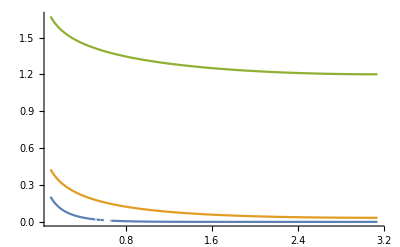

```mathematica
plot1=Plot[{V[th]/. { d->1,Iext->1,ri->1,c->0.25,tha->0.1},
V[th]/. { d->1,Iext->1,ri->1,c->1,tha->0.1},
V[th]/. { d->1,Iext->1,ri->1,c->4,tha->0.1}
},{th,0.1,Pi},PlotRange->All]
```

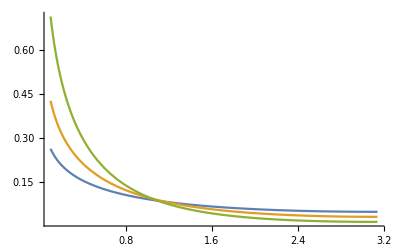

```mathematica
Plot[{V[th]//. { d->1,Iext->1,ri->0.5,c->1/Sqrt[ri],tha->0.1},
V[th]//. { d->1,Iext->1,ri->1,c->1/Sqrt[ri],tha->0.1},
V[th]//. { d->1,Iext->1,ri->2,c->1/Sqrt[ri],tha->0.1}
},{th,0.1,Pi},PlotRange->All]
```

```mathematica
pldat=Cases[plot1,Line[data_]:>data,-4];
Export["mma_plot1_"<>IntegerString[#2]<>".dat",#,"Table"]&~MapIndexed~pldat
```

{mma_plot1_1.dat,mma_plot1_2.dat,mma_plot1_3.dat,mma_plot1_4.dat,mma_plot1_5.dat,mma_plot1_6.dat,mma_plot1_7.dat,mma_plot1_8.dat,mma_plot1_9.dat}

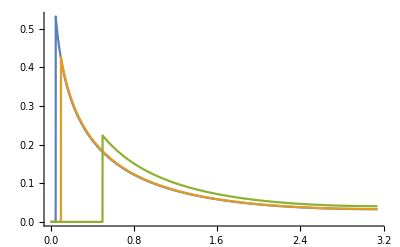

```mathematica
plot2=Plot[{V[th]*Boole[th>0.05]/. { d->1,Iext->1,ri->1,c->1,tha->0.05},
V[th]*Boole[th>0.1]/. { d->1,Iext->1,ri->1,c->1,tha->0.1},
V[th]*Boole[th>0.5]/. { d->1,Iext->1,ri->1,c->1,tha->0.5}
},{th,0.0,Pi},PlotRange->All]
```

```mathematica
pldat=Cases[plot2,Line[data_]:>data,-4];
Export["mma_plot2_"<>IntegerString[#2]<>".dat",#,"Table"]&~MapIndexed~pldat
```

{mma_plot2_1.dat,mma_plot2_2.dat,mma_plot2_3.dat}

#### Check leak

```mathematica
Ileak[tha_]:=2*Pi*d/(c*ri)*NIntegrate[V[th]*Sin[th],{th,tha,Pi}]
```

```mathematica
With[{tha=0.1},
Vnum[th_,tha_]=V[th]/.{ d->1,Iext->1,ri->10,c->5};
2*Pi*d/c^2/ri*NIntegrate[Vnum[th,tha]*Sin[th],{th,tha,Pi}]
]/.{ d->1,ri->10,c->5}
```

1.

```mathematica
Vpeak=PowerExpand[FullSimplify[PowerExpand[V[tha]]]]
```

(Iext ri (LegendreQ[-1/2-1/2 √(1-4/c^2),Cos[tha]]+LegendreQ[1/2 (-1+√(1-4/c^2)),Cos[tha]]))/(d π (-2 Cos[tha] (LegendreQ[1/2-1/2 √(1-4/c^2),1,Cos[tha]]+LegendreQ[1/2 (1+√(1-4/c^2)),1,Cos[tha]]) Sin[tha]+((-1+√(1-4/c^2)) LegendreQ[1/2-1/2 √(1-4/c^2),Cos[tha]]-(1+√(1-4/c^2)) LegendreQ[1/2 (1+√(1-4/c^2)),Cos[tha]]) Sin[tha]^2))

```mathematica
(* for c>4, the Q are real, so that is easier for series *)
```

```mathematica
Vpeaknum =FullSimplify[PowerExpand[Vpeak/.{ d->1,Iext->1,ri->1,c->5}]]
```

-((5 Csc[tha]^2 (LegendreQ[-1/2-(√21)/10,Cos[tha]]+LegendreQ[1/10 (-5+√21),Cos[tha]]))/(π (-(-5+√21) LegendreQ[1/2-(√21)/10,Cos[tha]]+(5+√21) LegendreQ[1/10 (5+√21),Cos[tha]]+10 Cot[tha] (LegendreQ[1/2-(√21)/10,1,Cos[tha]]+LegendreQ[1/10 (5+√21),1,Cos[tha]]))))

```mathematica
Vpeaknum /.tha->0.1
```

2.39103

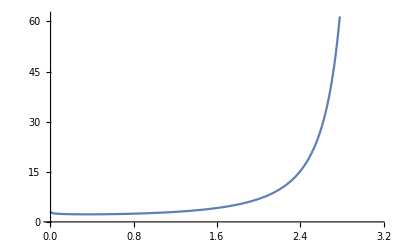

```mathematica
Plot[Vpeaknum,{tha,0.001,Pi}]
```

```mathematica
svn=Series[Vpeaknum,{tha,0,1},Assumptions->(tha>0)];
```

$Aborted

```mathematica
FullSimplify[Normal[svn]]
```

-1/(8 π)(HarmonicNumber[-3/4-(√21)/20]+HarmonicNumber[-1/4-(√21)/20]+HarmonicNumber[1/20 (-15+√21)]+HarmonicNumber[1/20 (-5+√21)]+4 Log[tha])

```mathematica
sv=Series[Vpeak,{tha,0,0},Assumptions->(tha>0)];
```

```mathematica
FullSimplify[Normal[sv]]
```

-1/(4 d π)Iext ri (HarmonicNumber[-1/2-1/2 √(1-4/c^2)]+HarmonicNumber[1/2 (-1+√(1-4/c^2))]-Log[4]+2 Log[tha])

```mathematica
Limit[%/Log[tha],tha->0]
```

-(Iext ri)/(2 d π)

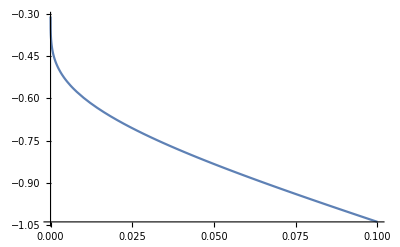

```mathematica
Plot[Re[Vpeaknum]/Log[tha],{tha,0,0.1}]
```

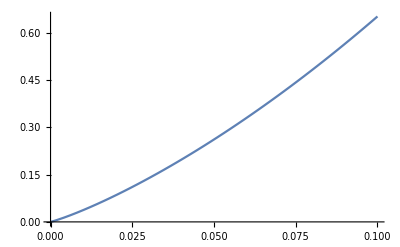

```mathematica
Plot[Re[Vpeaknum]*tha/Log[tha]*(-2*Pi),{tha,0,0.1}]
```

### Limit of large cells (small c)

```mathematica
Vn[th_]:=V[th]/. { d->1,Iext->1,ri->1,c->1/10,tha->1/100}
```

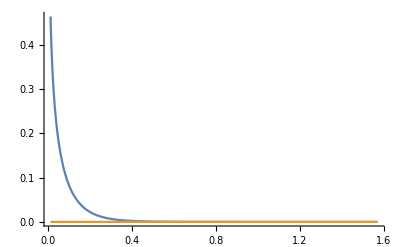

```mathematica
Plot[{Re[Vn[th]],Im[Vn[th]]},
{th,0.01,Pi/2},PlotRange->All]
```

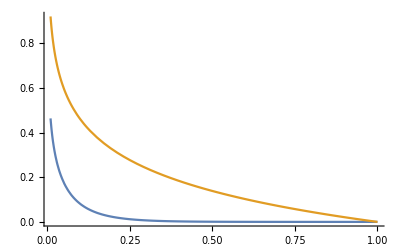

```mathematica
Plot[{Re[Vn[th]],-Log[th]/5},
{th,0.01,1},PlotRange->All]
```

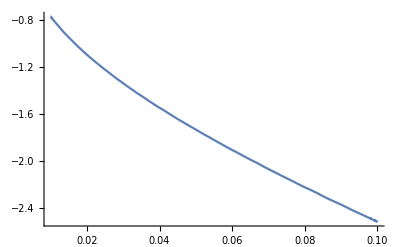

```mathematica
Plot[Log[Re[Vn[th]]],{th,0.01,0.1},PlotRange->All]
```

1) Given geometry, I expect : V=exp(-th)/th^2 ??
2) For smaller c (c<1/20) , things get very very weird. The BC is no longer satisfied.  Not sure where the problem comes from. Branch cut?

```mathematica
Vn[th_]:=V[th]/. { d->1,Iext->1,ri->1,c->1/30,tha->1/10}
```

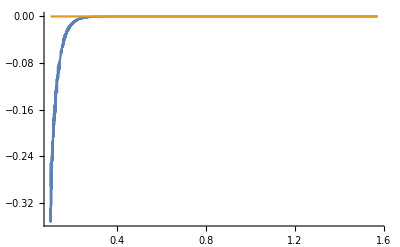

```mathematica
Plot[{Re[Vn[th]],Im[Vn[th]]},
{th,0.1,Pi/2},PlotRange->All]
```

```mathematica
Plot[Log[Re[Vn[th]]],{th,0.1,Pi/2},PlotRange->All]
```

-Graphics-

### Cable case for comparison

```mathematica
Clear["lamc"]
```

```mathematica
ll=Pi; (* so the plot limit is the same as above *)
vcss[x_]=FullSimplify[
Vc[x]/.DSolve[{
Vc[x]==lamc^2*Vc''[x],
Vc'[ll]==0,
Vc'[xa]==-4*ri/Pi/d^2},Vc[x],x][[1]]
]
```

(4 lamc ri Cosh[(π-x)/lamc] Csch[(π-xa)/lamc])/(d^2 π)

```mathematica
(*lamc=Sqrt[d*rm/(4*ri)];*)
```

```mathematica
vcssnum[x_]=(vcss[x] /. { d->1,Iext->1,ri->1})*Boole[x>xa]
```

(4 lamc Boole[x>xa] Cosh[(π-x)/lamc] Csch[(π-xa)/lamc])/π

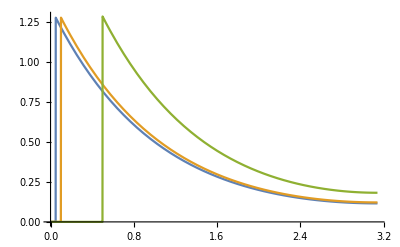

```mathematica
plot3=Plot[{
vcssnum[x]/.{xa->0.05,lamc->1},
vcssnum[x]/.{xa->0.1,lamc->1},
vcssnum[x]/.{xa->0.5,lamc->1}},
{x,0,Pi}]
```

```mathematica
pldat3=Cases[plot3,Line[data_]:>data,-4];
Export["mma_plot3_"<>IntegerString[#2]<>".dat",#,"Table"]&~MapIndexed~pldat3
```

{mma_plot3_1.dat,mma_plot3_2.dat,mma_plot3_3.dat}

```mathematica
vcss[xa]
```

(4 lamc ri Coth[(π-xa)/lamc])/(d^2 π)

### More limiting behavior

```mathematica
Needs["NumericalCalculus`"]
```

NLimit::shdw: Symbol NLimit appears in multiple contexts {NumericalCalculus`,Global`}; definitions in context NumericalCalculus` may shadow or be shadowed by other definitions.

```mathematica
Vpeak=PowerExpand[FullSimplify[PowerExpand[V[tha]]]]
```

```mathematica
Vpeakb [c_]=FullSimplify[PowerExpand[Vpeak/.{ d->1,Iext->1,ri->1}]]
```

(LegendreQ[-1/2-1/2 √(1-4/c^2),Cos[tha]]+LegendreQ[1/2 (-1+√(1-4/c^2)),Cos[tha]])/(π (((-1+√(1-4/c^2)) LegendreQ[1/2-1/2 √(1-4/c^2),Cos[tha]]-(1+√(1-4/c^2)) LegendreQ[1/2 (1+√(1-4/c^2)),Cos[tha]]) Sin[tha]^2-(LegendreQ[1/2-1/2 √(1-4/c^2),1,Cos[tha]]+LegendreQ[1/2 (1+√(1-4/c^2)),1,Cos[tha]]) Sin[2 tha]))

```mathematica
NLimit[Vpeakb[1]/Log[tha],tha->0]
```

Power::infy: Infinite expression 1/0. encountered.

NLimit::notnum: The expression ComplexInfinity is not numerical at the point tha == 1..

NLimit[(LegendreQ[-1/2-(ⅈ √3)/2,Cos[tha]]+LegendreQ[1/2 (-1+ⅈ √3),Cos[tha]])/(π Log[tha] (((-1+ⅈ √3) LegendreQ[1/2-(ⅈ √3)/2,Cos[tha]]-(1+ⅈ √3) LegendreQ[1/2 (1+ⅈ √3),Cos[tha]]) Sin[tha]^2-(LegendreQ[1/2-(ⅈ √3)/2,1,Cos[tha]]+LegendreQ[1/2 (1+ⅈ √3),1,Cos[tha]]) Sin[2 tha])),tha→0]

```mathematica
NLimit[Vpeakb[1]*tha,tha->0]
Limit[Vpeakb[1]*tha,tha->0]
```

7.95149×10^-7+0. ⅈ

lim_(tha→0) (tha (LegendreQ[-1/2-(ⅈ √3)/2,Cos[tha]]+LegendreQ[1/2 (-1+ⅈ √3),Cos[tha]]))/(π (((-1+ⅈ √3) LegendreQ[1/2-(ⅈ √3)/2,Cos[tha]]-(1+ⅈ √3) LegendreQ[1/2 (1+ⅈ √3),Cos[tha]]) Sin[tha]^2-(LegendreQ[1/2-(ⅈ √3)/2,1,Cos[tha]]+LegendreQ[1/2 (1+ⅈ √3),1,Cos[tha]]) Sin[2 tha]))

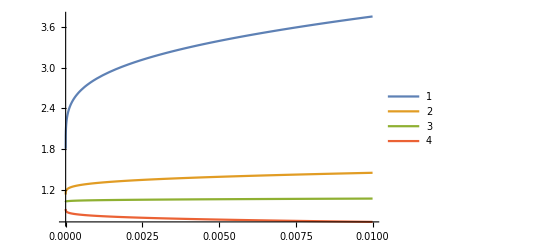

```mathematica
Plot[{-Vpeakb[5]*2*Pi/Log[tha],
-Vpeakb[2]*2*Pi/Log[tha],
-Vpeakb[1]*2*Pi/Log[tha],
-Vpeakb[0.25]*2*Pi/Log[tha]
},{tha,0,0.01},PlotLegends->Automatic]
```

```mathematica
Plot3D[Vpeakb[c]/Log[tha],{c,0.1,10},{tha,0,0.1}]
```

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

-Graphics3D-

```mathematica
Limit[Vpeakb[1]/Log[tha],tha->0]
```

Indeterminate

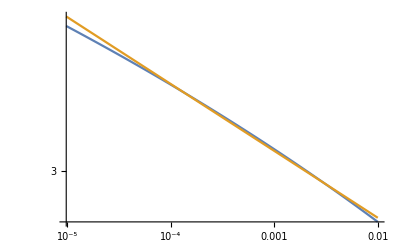

```mathematica
LogLogPlot[{Vpeakb[5], 2.2*tha^-0.05},{tha,0,0.01}]
```

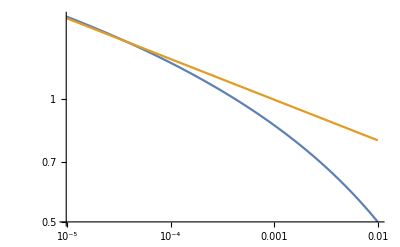

```mathematica
LogLogPlot[{Vpeakb[1/5],0.5* tha^-0.1},{tha,0,0.01}]
```

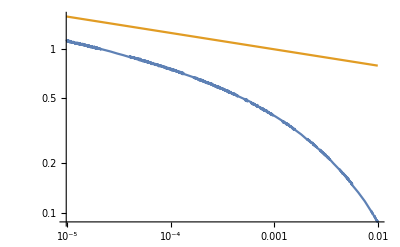

```mathematica
LogLogPlot[{Vpeakb[1/100],0.5* tha^-0.1},{tha,0,0.01}]
```

```mathematica
Limit[Vpeakb[c],c->0]
```

lim_(c→0) (LegendreQ[-1/2-1/2 √(1-4/c^2),Cos[tha]]+LegendreQ[1/2 (-1+√(1-4/c^2)),Cos[tha]])/(π (((-1+√(1-4/c^2)) LegendreQ[1/2-1/2 √(1-4/c^2),Cos[tha]]-(1+√(1-4/c^2)) LegendreQ[1/2 (1+√(1-4/c^2)),Cos[tha]]) Sin[tha]^2-(LegendreQ[1/2-1/2 √(1-4/c^2),1,Cos[tha]]+LegendreQ[1/2 (1+√(1-4/c^2)),1,Cos[tha]]) Sin[2 tha]))

### Realistic parameters (see p.17/p28) : rho=40, c=lam/rho = ~ 10, theta_a = 0.05, rho=40, c=lam/rho =55, theta_a = 0.025,

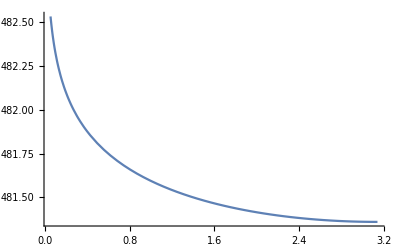

```mathematica
Plot[{V[th]/. { d->0.5,Iext->1,ri->1,c->55,tha->0.025}},{th,0.05,Pi},PlotRange->All]
```

```mathematica
Rin=ri*c^2/(4*Pi*d) (* single comp. result*)(* see p.32 *)
Rin/. { d->0.5,ri->10^6,c->55,tha->0.25}
```

(c^2 ri)/(4 d π)

4.81444×10^8

```mathematica
RinCorrection=FullSimplify[ PowerExpand[FullSimplify[ PowerExpand[V[tha]/Rin/Iext]]]]
FullSimplify[%/. { d->0.5,ri->10^6,c->55,tha->0.025}   ]
```

-((4 Csc[tha]^2 (LegendreQ[-1/2-1/2 √(1-4/c^2),Cos[tha]]+LegendreQ[1/2 (-1+√(1-4/c^2)),Cos[tha]]))/(c^2 ((1-√(1-4/c^2)) LegendreQ[1/2-1/2 √(1-4/c^2),Cos[tha]]+(1+√(1-4/c^2)) LegendreQ[1/2 (1+√(1-4/c^2)),Cos[tha]]+2 Cot[tha] (LegendreQ[1/2-1/2 √(1-4/c^2),1,Cos[tha]]+LegendreQ[1/2 (1+√(1-4/c^2)),1,Cos[tha]]))))

1.00272

```mathematica
V[0.05]/V[Pi-0.001]/. { d->1,Iext->1,ri->1,c->10}
```

1.07436

```mathematica
V[th1]/V[th2]
```

(LegendreQ[-1/2-1/2 √(1-4/c^2),Cos[th1]]+LegendreQ[-1/2+1/2 √(1-4/c^2),Cos[th1]])/(LegendreQ[-1/2-1/2 √(1-4/c^2),Cos[th2]]+LegendreQ[-1/2+1/2 √(1-4/c^2),Cos[th2]])

```mathematica
(* input resistance for a compact sphere *)
```

### Double limit

```mathematica
Vpeak=PowerExpand[FullSimplify[PowerExpand[V[tha]]]];
```

```mathematica
Vpeakb [c_]=FullSimplify[PowerExpand[Vpeak/.{ d->1,Iext->1,ri->1}]]
```

(LegendreQ[-1/2-1/2 √(1-4/c^2),Cos[tha]]+LegendreQ[1/2 (-1+√(1-4/c^2)),Cos[tha]])/(π (((-1+√(1-4/c^2)) LegendreQ[1/2-1/2 √(1-4/c^2),Cos[tha]]-(1+√(1-4/c^2)) LegendreQ[1/2 (1+√(1-4/c^2)),Cos[tha]]) Sin[tha]^2-(LegendreQ[1/2-1/2 √(1-4/c^2),1,Cos[tha]]+LegendreQ[1/2 (1+√(1-4/c^2)),1,Cos[tha]]) Sin[2 tha]))

```mathematica
(* when is peak twice the minimal value? 
Presumable this will always happen for some small theta, but presumably smaller and smaller for larger 'c' (more compact) *)
```

```mathematica
vmin[c_]=FullSimplify[PowerExpand[FullSimplify[PowerExpand[V[Pi-10^-4]/.{ d->1,Iext->1,ri->1}]]]]
```

(LegendreQ[-1/2-1/2 √(1-4/c^2),-1]+LegendreQ[1/2 (-1+√(1-4/c^2)),-1])/(π (((-1+√(1-4/c^2)) LegendreQ[1/2-1/2 √(1-4/c^2),Cos[tha]]-(1+√(1-4/c^2)) LegendreQ[1/2 (1+√(1-4/c^2)),Cos[tha]]) Sin[tha]^2-(LegendreQ[1/2-1/2 √(1-4/c^2),1,Cos[tha]]+LegendreQ[1/2 (1+√(1-4/c^2)),1,Cos[tha]]) Sin[2 tha]))

```mathematica
Solve[Vpeakb[c]==2*vmin[c],tha]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[(LegendreQ[-1/2-1/2 √(1-4/c^2),Cos[tha]]+LegendreQ[1/2 (-1+√(1-4/c^2)),Cos[tha]])/(π (((-1+√(1-4/c^2)) LegendreQ[1/2-1/2 √(1-4/c^2),Cos[tha]]-(1+√(1-4/c^2)) LegendreQ[1/2 (1+√(1-4/c^2)),Cos[tha]]) Sin[tha]^2-(LegendreQ[1/2-1/2 √(1-4/c^2),1,Cos[tha]]+LegendreQ[1/2 (1+√(1-4/c^2)),1,Cos[tha]]) Sin[2 tha]))==(2 (LegendreQ[-1/2-1/2 √(1-4/c^2),-1]+LegendreQ[1/2 (-1+√(1-4/c^2)),-1]))/(π (((-1+√(1-4/c^2)) LegendreQ[1/2-1/2 √(1-4/c^2),Cos[tha]]-(1+√(1-4/c^2)) LegendreQ[1/2 (1+√(1-4/c^2)),Cos[tha]]) Sin[tha]^2-(LegendreQ[1/2-1/2 √(1-4/c^2),1,Cos[tha]]+LegendreQ[1/2 (1+√(1-4/c^2)),1,Cos[tha]]) Sin[2 tha])),tha]

```mathematica
NSolve[Vpeakb[4]==2*vmin[4],tha]
```

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

{{}}

```mathematica
thcrit[cp_]:=tha/.FindRoot[(LegendreQ[-1/2-1/2 √(1-4/c^2),Cos[tha]]+LegendreQ[1/2 (-1+√(1-4/c^2)),Cos[tha]])==(2 (LegendreQ[-1/2-1/2 √(1-4/c^2),-0.9999]+LegendreQ[1/2 (-1+√(1-4/c^2)),-0.9999]))/.c->cp,{tha,0.1}][[1]]
```

```mathematica
thcrit[4]
```

-0.00103191

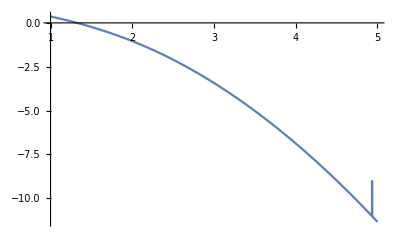

```mathematica
Plot[Log[Abs[thcrit[c]]],{c,1,5}]
```